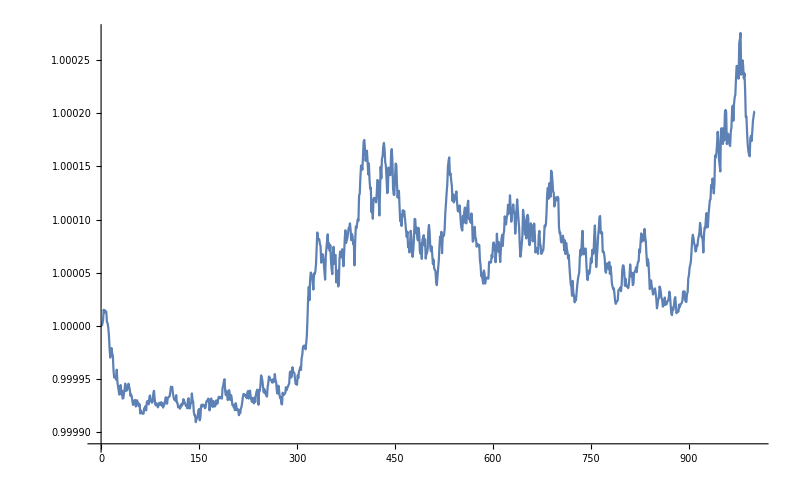

```mathematica
d1=Flatten@ToExpression@StringSplit[Import["./logode"],","];
d2 = Flatten@ToExpression@StringSplit[Import["./parabola"],","];
ListLinePlot[{d1,d2}]
```

```mathematica
d[k_]:=Flatten@ToExpression@StringSplit[Import["./BENCHMARK"][[k]],","]
```

Rule::rhs: Pattern log_ode appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,{{{1.,0.06},{2.,0.0575908},{3.,0.0555069},{4.,0.0537261},{5.,0.0501651},{6.,0.0484955},{7.,0.0456608},{8.,0.0453094},{9.,0.0445602},{10.,0.0471641},{11.,0.0473271},«30»,{42.,0.0652511},{43.,0.0641189},{44.,0.0596043},{45.,0.056917},{46.,0.0583747},{47.,0.0651222},{48.,0.0657602},{49.,0.0622298},{50.,0.0644868},«952»},«3»},Charting`Private`Tag$3975]→{«1»}.

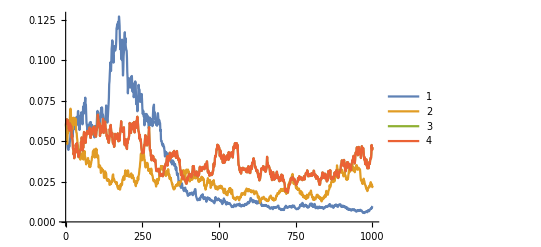

```mathematica
ListLinePlot[Table[d[k],{k,2,5}],PlotLegends->Automatic]
```

```mathematica
Table[d[k],{k,2,5}]
```

{{0.06,0.0614226,0.0611073,0.0588825,0.0573253,0.0586116,0.0591704,0.0591107,0.0563882,0.0577166,0.0586755,0.0617436,0.0605318,0.0597067,0.0574266,0.0515284,0.0493741,0.049298,0.0485425,0.0470809,0.0439518,0.0437134,0.0454719,0.0473393,0.0462531,0.0501419,0.0485614,0.0439004,0.0425939,0.0415048,0.0412986,0.0399658,0.03816,0.0378008,0.0389332,0.0390047,0.0376907,0.0353978,0.0350491,0.0364335,0.0393243,0.0399848,0.0404386,0.0441494,0.0447388,0.0437294,0.0472638,0.0447861,0.0411594,0.0419069,0.0435482,0.0415154,0.042089,0.0404091,0.0419787,0.0403031,0.0383909,0.0408405,0.03942,0.0428661,0.040284,0.0407542,0.0425952,0.0432938,0.0420986,0.0428462,0.0429375,0.0415206,0.0432389,0.0452104,0.0439039,0.0427996,0.0435868,0.041484,0.045326,0.0454441,0.0484277,0.0472652,0.0486527,0.0497121,0.0501111,0.0502345,0.0482299,0.0476165,0.0482528,0.0480214,0.0480214,0.052081,0.0534609,0.0540199,0.0527219,0.051462,0.0479059,0.0533569,0.0520748,0.0561879,0.0608437,0.0619653,0.0630531,0.0616024,0.06316,0.0687907,0.0682834,0.0661728,0.0671076,0.0687537,0.0700736,0.0732181,0.0772284,0.0868647,0.0919362,0.0837378,0.0879934,0.0891186,0.0869861,0.0906417,0.0940961,0.0917477,0.0873868,0.0854605,0.0857952,0.0893605,0.0828025,0.0790823,0.0772849,0.0728473,0.0747722,0.0748168,0.065622,0.0688758,0.074343,0.0739498,0.0765832,0.0734827,0.0733248,0.0728673,0.074209,0.0737871,0.0761195,0.0759983,0.0762474,0.0739349,0.076782,0.0802257,0.0841263,0.0777646,0.0778498,0.0781793,0.0754847,0.0760419,0.0755635,0.0738421,0.0729093,0.0737173,0.0677661,0.0725789,0.0714803,0.0727172,0.0685698,0.0710135,0.0732645,0.0728437,0.0728706,0.0739123,0.0712085,0.0733254,0.0735595,0.0691723,0.0733564,0.0746947,0.0762258,0.0845322,0.0896564,0.0864552,0.0870183,0.0846413,0.0829175,0.0812484,0.0806076,0.0788442,0.0796847,0.0750419,0.0724242,0.0753224,0.0756684,0.0770497,0.0791786,0.0785497,0.0782191,0.0809342,0.0806336,0.0772544,0.0731649,0.0709664,0.068145,0.0695486,0.0677768,0.0682149,0.0673179,0.0620329,0.0581031,0.0543218,0.0530943,0.0567194,0.0574204,0.0551809,0.0485135,0.0498723,0.0543959,0.0543809,0.0550545,0.0590741,0.0647003,0.0607217,0.0595514,0.0600575,0.0585867,0.0638657,0.0585787,0.0581266,0.0567039,0.0567258,0.0618588,0.0633505,0.0621673,0.0640927,0.0628994,0.0683573,0.0643429,0.0621831,0.0611895,0.0636888,0.0617803,0.0619154,0.061788,0.058652,0.056509,0.0580325,0.0563811,0.0563497,0.0547656,0.0534039,0.0511232,0.0519152,0.0479077,0.05117,0.052237,0.0536144,0.0548185,0.0551986,0.0565151,0.0527475,0.0528468,0.0568757,0.0550774,0.0538024,0.0532027,0.0532353,0.0518883,0.0514014,0.0527684,0.0494059,0.0482731,0.0484625,0.0446213,0.0449812,0.0460914,0.0455128,0.0462071,0.0455192,0.0485342,0.0553262,0.0575497,0.0597983,0.0613765,0.0594291,0.0603538,0.0616186,0.0549597,0.0551309,0.0552555,0.0596056,0.060288,0.0586512,0.0544393,0.0551881,0.0544672,0.0601654,0.0615101,0.0675098,0.0646938,0.0673951,0.0678249,0.0658366,0.0718396,0.0734427,0.0715687,0.0682625,0.0676096,0.0727305,0.0738637,0.0673487,0.0686909,0.0678592,0.073509,0.0798596,0.0793716,0.0819115,0.0810771,0.0817108,0.0870565,0.08199,0.0799781,0.0754654,0.0765145,0.0753242,0.0712419,0.0671591,0.0704851,0.0736131,0.0796039,0.0792547,0.0769543,0.0779973,0.0770151,0.0732088,0.0708162,0.0716879,0.0712573,0.0770417,0.0744088,0.0765823,0.0748544,0.0798673,0.0868397,0.0887857,0.0924641,0.0977744,0.0965574,0.096626,0.0943727,0.0900953,0.089458,0.0869641,0.0834126,0.0918164,0.0870252,0.0806691,0.0828534,0.0781162,0.0716487,0.066861,0.0685529,0.0648559,0.0655211,0.0675849,0.0638315,0.0640512,0.0678043,0.0632754,0.0627252,0.0686817,0.0665408,0.0644487,0.0616935,0.0593744,0.058597,0.0591567,0.05507,0.0544816,0.0579877,0.0626024,0.0597542,0.0572928,0.0552409,0.0508495,0.0489537,0.0492342,0.0489488,0.050623,0.0504144,0.0548284,0.0546615,0.0569751,0.0557592,0.0560682,0.0571086,0.0557656,0.0554196,0.0519775,0.0485014,0.048594,0.0495257,0.0463672,0.0454334,0.0450131,0.0439396,0.0453106,0.0433556,0.0444626,0.0440342,0.0470477,0.0483947,0.0488823,0.0447164,0.044188,0.0445199,0.0424107,0.0440052,0.0441018,0.0409606,0.0432591,0.0436676,0.0449613,0.0482485,0.0496322,0.0510822,0.0532979,0.0541228,0.0554555,0.0550156,0.0576557,0.0602347,0.0582093,0.0597363,0.0607854,0.0606202,0.056977,0.0575508,0.0525951,0.0556396,0.0575987,0.0506773,0.0460547,0.045544,0.0475266,0.049136,0.0496027,0.0485585,0.0497877,0.0493813,0.0494106,0.0487854,0.0508398,0.0544008,0.0529868,0.0502161,0.0500255,0.0501046,0.0485398,0.0502955,0.0524105,0.0540524,0.0517368,0.0520565,0.0481542,0.0474826,0.0489597,0.0510863,0.0512237,0.054203,0.0602208,0.0599944,0.0573938,0.0571085,0.0607255,0.0584921,0.0637093,0.064578,0.0626106,0.0625397,0.0656036,0.0707907,0.0706619,0.0704988,0.0741202,0.0728909,0.0697356,0.0710476,0.0675386,0.0635488,0.0665515,0.0655774,0.0649349,0.0625846,0.0606828,0.0567411,0.0570411,0.0606444,0.0645111,0.0632171,0.0647098,0.0652233,0.0631651,0.0665297,0.0628387,0.0636981,0.0647474,0.0606593,0.0593297,0.0686966,0.0658694,0.0681758,0.0682019,0.0715082,0.0737605,0.0715989,0.0770379,0.0752311,0.0784027,0.0749911,0.071654,0.0705949,0.0651682,0.061225,0.0601754,0.0612903,0.058623,0.0575504,0.0572494,0.0608289,0.0621183,0.062827,0.0575577,0.0626315,0.0617218,0.0635841,0.0691336,0.0695789,0.0675467,0.0692771,0.0660936,0.0645318,0.0655248,0.066865,0.0629679,0.0624898,0.0588402,0.0572765,0.0547717,0.0540309,0.0532434,0.0526682,0.0480285,0.0463895,0.0430761,0.0418164,0.0412573,0.0395067,0.0392169,0.0403247,0.0402675,0.0434377,0.0435128,0.0432636,0.0443279,0.0447098,0.0441858,0.0437052,0.039857,0.0399813,0.0366253,0.0358048,0.0377701,0.0404163,0.0437493,0.0441913,0.0447166,0.0447826,0.0466699,0.0472561,0.0504421,0.0498559,0.0462096,0.0461774,0.0484571,0.0474621,0.0450817,0.0417742,0.040096,0.0435103,0.043831,0.0451235,0.0435057,0.0439407,0.0420271,0.0431757,0.043344,0.042198,0.0430084,0.0418484,0.0404037,0.0397173,0.0367438,0.0375215,0.0399097,0.0373356,0.037194,0.0384088,0.0407055,0.0401289,0.0403708,0.0384669,0.0413296,0.0401257,0.0397674,0.0404894,0.0412198,0.0395832,0.0371296,0.0388613,0.0381913,0.0399505,0.0407429,0.0390787,0.0358295,0.0375125,0.0392851,0.0397658,0.0392236,0.0386027,0.0375061,0.037303,0.0351496,0.0359412,0.0357311,0.0372146,0.0350381,0.0318926,0.0353153,0.0326051,0.035335,0.0330459,0.035249,0.0336867,0.0350782,0.0342287,0.0347238,0.0338408,0.0333756,0.0337836,0.0364283,0.0348127,0.034971,0.0314918,0.029127,0.0273978,0.0278753,0.0249514,0.02586,0.0279299,0.0297389,0.0275623,0.028864,0.0293405,0.0295179,0.027706,0.028008,0.0285522,0.0299824,0.0319561,0.0307703,0.0316014,0.0292494,0.0277683,0.026861,0.0265991,0.0272563,0.0244425,0.0238432,0.0233173,0.0228615,0.0209434,0.0204443,0.0203433,0.0219835,0.0221024,0.0220255,0.0250228,0.0263333,0.0265755,0.0261835,0.0262654,0.0260197,0.0258642,0.0267599,0.0257382,0.0254177,0.0248181,0.0257795,0.0262345,0.027441,0.0246134,0.0247955,0.025256,0.0250733,0.0237554,0.0242247,0.0245677,0.0259458,0.0255901,0.0251969,0.0240845,0.0261484,0.0238137,0.0232638,0.0222763,0.0221011,0.0220605,0.0224916,0.022431,0.0207985,0.0196216,0.0205772,0.0185151,0.017709,0.0183475,0.0187928,0.0179701,0.0156065,0.016732,0.0163691,0.0158726,0.0159865,0.0147398,0.0144451,0.0147068,0.0139968,0.0143555,0.014416,0.0135705,0.0138648,0.0134046,0.0128618,0.013543,0.0128772,0.0139606,0.014428,0.013976,0.0143019,0.0150524,0.0136231,0.0134715,0.0128293,0.0131937,0.0131425,0.012951,0.0124036,0.0126168,0.0123454,0.0112907,0.010827,0.0118308,0.0127009,0.012898,0.0135778,0.0136035,0.0141418,0.0134614,0.0134321,0.0127015,0.0138434,0.0138122,0.0137653,0.0132195,0.0137195,0.0139432,0.0148422,0.0148951,0.0148692,0.014115,0.0145292,0.0158634,0.0164101,0.0168905,0.0167589,0.0163241,0.0156854,0.0154194,0.0161258,0.0153165,0.0153024,0.0164431,0.0167721,0.0165694,0.015593,0.0156625,0.0144658,0.0142386,0.0146109,0.0140886,0.0134694,0.0136283,0.0124688,0.0125763,0.0127087,0.0125174,0.0122978,0.0116671,0.0121796,0.012326,0.012076,0.0111794,0.0117348,0.0114897,0.0116865,0.0123371,0.0120134,0.01222,0.0117068,0.0121658,0.0123782,0.012608,0.0117787,0.0121705,0.0124237,0.0130437,0.0121293,0.0122258,0.0120256,0.0118221,0.0115485,0.0126898,0.0118879,0.011745,0.0113879,0.0118528,0.0123423,0.0121979,0.0117719,0.0121349,0.0118428,0.0132958,0.0130113,0.0127473,0.0120125,0.0118902,0.0124837,0.0119425,0.0119938,0.012025,0.0124416,0.0118659,0.0124992,0.012405,0.013124,0.0134306,0.0141487,0.0137374,0.0148463,0.0149696,0.0156114,0.0143621,0.014099,0.0142697,0.013717,0.0136998,0.0130803,0.0142196,0.0137842,0.0143799,0.0135686,0.0128651,0.0135926,0.0133894,0.0129435,0.0130943,0.0132077,0.0133227,0.0140596,0.0136802,0.0129857,0.013241,0.0127185,0.0137817,0.0128239,0.0131723,0.0131642,0.0125579,0.0118002,0.0118719,0.0113686,0.011146,0.0113556,0.011758,0.0119775,0.0112276,0.0112075,0.0108811,0.0111472,0.0113719,0.0109797,0.0111821,0.011026,0.0101316,0.0103111,0.00977763,0.0103334,0.0112079,0.0110057,0.0111212,0.0105136,0.01171,0.0117512,0.0112378,0.0114025,0.0112454,0.0121067,0.0118665,0.0116412,0.0107573,0.0111922,0.0108556,0.0104029,0.010681,0.0106707,0.0103849,0.0108855,0.0105796,0.010898,0.0109035,0.0101879,0.00993103,0.0107747,0.0113457,0.0120394,0.0115953,0.0113781,0.0119718,0.012738,0.0119522,0.0114621,0.0112133,0.0102283,0.0100945,0.010299,0.0111037,0.0117823,0.0115479,0.0111751,0.0111639,0.012132,0.012763,0.0129714,0.0131148,0.0134555,0.012644,0.0131991,0.0136987,0.0140086,0.0136693,0.0130776,0.0131254,0.0131816,0.0129816,0.0122918,0.0117139,0.0119537,0.0122831,0.0121675,0.011946,0.0124371,0.0127796,0.0122805,0.0131196,0.0127511,0.0133734,0.0136573,0.0131667,0.0146883,0.0154201,0.0160014,0.0152401,0.0156468,0.0163658,0.0170315,0.0175247,0.0176164,0.0177421,0.0185785,0.0186456,0.0187202,0.0189465,0.0204396,0.020539,0.0226573,0.0240726,0.0223511,0.0212609,0.0211982,0.0207176,0.0203242,0.018788,0.0191068,0.0178959,0.0169213,0.01636,0.0160217,0.0167869,0.015344,0.0149071,log_ode},{0.06,0.0587522,0.0579532,0.0554396,0.0542999,0.0486482,0.0479036,0.0504789,0.0542042,0.0515423,0.0522498,0.0503657,0.0499346,0.0481139,0.047888,0.0499476,0.0515839,0.0584117,0.061941,0.0645167,0.0660357,0.0685253,0.0653455,0.0656011,0.0683107,0.0663833,0.0657991,0.0661972,0.0618437,0.0612878,0.0682079,0.0678447,0.0709645,0.0713061,0.0772861,0.0776913,0.078595,0.0737668,0.0777098,0.0800632,0.0761644,0.0783816,0.0796224,0.0749794,0.0710523,0.0647386,0.067363,0.0660284,0.0681551,0.062089,0.0688841,0.0649708,0.0621866,0.0618705,0.0588294,0.0618658,0.0658807,0.0662216,0.0678174,0.0656586,0.0675262,0.0656727,0.0626103,0.0635315,0.0636815,0.0631474,0.0672816,0.066777,0.0700522,0.0726225,0.0717246,0.0772441,0.0794463,0.0842098,0.0862559,0.0864527,0.0813815,0.0825458,0.0828104,0.0863305,0.0901354,0.0932437,0.0994646,0.101304,0.0957121,0.0895516,0.0951055,0.0945887,0.0946265,0.0933837,0.101403,0.101082,0.0974199,0.0965743,0.102676,0.0979173,0.0885502,0.0878988,0.0902553,0.0889196,0.0881143,0.0862467,0.0850745,0.0875452,0.0839162,0.0821795,0.0855405,0.0862543,0.0847811,0.0877069,0.0847306,0.0904021,0.0904435,0.0885834,0.0982561,0.10497,0.102338,0.101039,0.0960976,0.0910333,0.0886607,0.0892802,0.0950324,0.0922287,0.0953972,0.0933164,0.092305,0.0960021,0.0978907,0.0963802,0.0974089,0.107992,0.103552,0.103595,0.102661,0.0998579,0.102366,0.110742,0.110138,0.117463,0.119399,0.131843,0.126698,0.120684,0.118489,0.11911,0.113811,0.115035,0.116047,0.108672,0.108235,0.113501,0.119272,0.122772,0.130639,0.126409,0.125798,0.125777,0.12909,0.128621,0.134535,0.128756,0.119282,0.124563,0.129623,0.139225,0.139336,0.13546,0.132838,0.124284,0.122924,0.117475,0.113144,0.111729,0.113868,0.118576,0.117257,0.110039,0.109588,0.107164,0.103131,0.106596,0.10963,0.0987311,0.102415,0.0987252,0.0989087,0.0987338,0.100927,0.103468,0.0991347,0.101471,0.101769,0.102116,0.105675,0.103814,0.103187,0.0974596,0.0971704,0.105611,0.10874,0.110472,0.126023,0.132181,0.138249,0.123191,0.126808,0.133635,0.130036,0.134514,0.121724,0.126978,0.119792,0.121257,0.125556,0.131601,0.134043,0.133469,0.145606,0.144044,0.148705,0.155948,0.163415,0.157775,0.162091,0.149679,0.138709,0.132474,0.139058,0.144469,0.14816,0.146808,0.143685,0.140276,0.130217,0.12844,0.128365,0.142602,0.139782,0.140065,0.144189,0.13388,0.13798,0.145993,0.156663,0.154338,0.143232,0.145344,0.134311,0.125116,0.129457,0.123474,0.125098,0.127112,0.136721,0.138103,0.149924,0.17089,0.169137,0.164448,0.177186,0.169356,0.186873,0.194779,0.179623,0.167642,0.165453,0.169381,0.160859,0.169746,0.164077,0.161101,0.156303,0.164861,0.164977,0.155803,0.154968,0.144256,0.139453,0.134913,0.137067,0.137682,0.12864,0.132109,0.129054,0.134265,0.14563,0.136184,0.13769,0.136586,0.147034,0.159156,0.157331,0.149953,0.15391,0.162416,0.159875,0.162957,0.164531,0.159305,0.171982,0.174402,0.181486,0.183215,0.181298,0.184514,0.180657,0.181879,0.195803,0.204387,0.211105,0.22051,0.221113,0.225276,0.233525,0.217139,0.219274,0.226393,0.217788,0.224074,0.240099,0.226876,0.24544,0.229248,0.225038,0.240271,0.233579,0.228183,0.218634,0.215063,0.212894,0.206368,0.189974,0.195036,0.201739,0.190551,0.188936,0.20162,0.198601,0.189853,0.200492,0.211535,0.196936,0.187257,0.195648,0.177212,0.18906,0.181346,0.190799,0.188843,0.175772,0.185629,0.193297,0.189749,0.191641,0.194977,0.200915,0.201931,0.20165,0.207593,0.204107,0.204609,0.19084,0.194284,0.185426,0.17804,0.171707,0.164068,0.162269,0.164693,0.165237,0.161509,0.159601,0.159567,0.151703,0.151428,0.149584,0.146528,0.147286,0.152482,0.159222,0.167226,0.16802,0.166723,0.166677,0.170724,0.161146,0.151191,0.152777,0.152838,0.16444,0.156364,0.14849,0.15094,0.15212,0.145349,0.143395,0.14696,0.15124,0.147225,0.140274,0.135141,0.129511,0.128889,0.118117,0.115295,0.11215,0.112964,0.106162,0.102553,0.103097,0.104072,0.104682,0.106052,0.107917,0.115134,0.112234,0.110756,0.107905,0.116003,0.121142,0.11428,0.104265,0.0997753,0.106173,0.103566,0.0966978,0.0950703,0.0914974,0.0948814,0.0981462,0.0992835,0.10118,0.101861,0.103331,0.111129,0.106495,0.103585,0.0985068,0.0917165,0.0990026,0.106008,0.109348,0.106959,0.104064,0.111805,0.10685,0.098626,0.0977947,0.0974569,0.0986658,0.0935749,0.0923481,0.0903765,0.0935825,0.100322,0.0995759,0.0983755,0.101304,0.098258,0.0995268,0.102286,0.102228,0.109336,0.114215,0.11275,0.113659,0.110416,0.104672,0.110705,0.103359,0.0994843,0.0995124,0.0993429,0.09651,0.0984721,0.0992627,0.107742,0.105303,0.107292,0.100583,0.0976237,0.0991397,0.0998677,0.093416,0.094427,0.0966019,0.102159,0.113294,0.106617,0.100854,0.0970501,0.0955635,0.10311,0.101174,0.104101,0.107361,0.106988,0.0996873,0.105641,0.114281,0.108645,0.11488,0.121701,0.132187,0.133821,0.136424,0.128313,0.131291,0.133537,0.125168,0.116406,0.111923,0.101565,0.103944,0.104559,0.105739,0.109993,0.105367,0.108625,0.108602,0.118105,0.116036,0.125205,0.129104,0.132702,0.13847,0.145366,0.156423,0.156796,0.159418,0.162141,0.16166,0.161752,0.158391,0.163567,0.165067,0.163452,0.169965,0.185904,0.179502,0.162801,0.165191,0.164852,0.16716,0.168894,0.178815,0.172946,0.18985,0.191345,0.18902,0.191018,0.184172,0.185321,0.178917,0.196318,0.194006,0.182141,0.165367,0.156889,0.151934,0.145332,0.141363,0.145814,0.138324,0.139114,0.134461,0.132546,0.137329,0.135147,0.131312,0.128433,0.136788,0.140935,0.13529,0.142792,0.151118,0.145981,0.145031,0.161129,0.169545,0.165991,0.179458,0.181975,0.201257,0.211427,0.215991,0.220159,0.2104,0.210559,0.200069,0.195308,0.191535,0.187906,0.20127,0.204151,0.195067,0.196045,0.187286,0.169685,0.172183,0.17764,0.180834,0.168826,0.163698,0.169971,0.171664,0.163611,0.166941,0.165417,0.150022,0.149551,0.146619,0.147604,0.148838,0.135486,0.125385,0.123679,0.124121,0.1265,0.131558,0.131184,0.13,0.13498,0.127457,0.127959,0.135178,0.134169,0.127664,0.118697,0.124618,0.123633,0.118239,0.121632,0.123865,0.127293,0.123763,0.1225,0.12243,0.124937,0.126109,0.113286,0.116841,0.124217,0.139955,0.135895,0.139169,0.147259,0.157397,0.152633,0.139427,0.141161,0.147896,0.14112,0.128814,0.131501,0.132166,0.124794,0.133584,0.133524,0.139277,0.142567,0.143736,0.141916,0.132211,0.133024,0.140854,0.146811,0.142582,0.148339,0.144267,0.134002,0.134206,0.136876,0.1334,0.14023,0.139695,0.142648,0.15349,0.165353,0.166581,0.178159,0.188397,0.184944,0.187638,0.181976,0.179668,0.172565,0.164826,0.159994,0.162325,0.174927,0.173305,0.157398,0.163302,0.161425,0.162183,0.147023,0.149853,0.145832,0.152184,0.150296,0.154923,0.144377,0.141381,0.130928,0.129158,0.116497,0.118791,0.115117,0.10415,0.0946112,0.0982123,0.0939598,0.0985961,0.101413,0.0977115,0.0963097,0.0988392,0.098479,0.0941154,0.0967,0.0955025,0.0999976,0.100815,0.0917352,0.0956302,0.100485,0.0999305,0.103261,0.0937984,0.100832,0.0952663,0.0955474,0.0970286,0.0986106,0.0983246,0.0985484,0.0968829,0.0998773,0.104466,0.0987508,0.0964493,0.089774,0.0964559,0.0986189,0.104814,0.101646,0.101918,0.104293,0.111266,0.10797,0.115427,0.12296,0.127046,0.126507,0.126061,0.121872,0.126021,0.120789,0.125571,0.137053,0.124566,0.130267,0.145842,0.138387,0.143843,0.148671,0.139905,0.1296,0.122626,0.116481,0.110292,0.110867,0.113506,0.118341,0.127246,0.125136,0.121891,0.13865,0.131232,0.123004,0.124365,0.127805,0.129517,0.126956,0.129717,0.137246,0.141372,0.135628,0.141106,0.150333,0.158049,0.152192,0.149717,0.154204,0.149602,0.147504,0.147201,0.159152,0.158957,0.166428,0.163533,0.162578,0.155317,0.148972,0.146855,0.145754,0.143595,0.149136,0.143244,0.132835,0.133454,0.132677,0.132665,0.139743,0.139336,0.12935,0.129537,0.135176,0.136674,0.152357,0.146896,0.14335,0.132127,0.125445,0.129314,0.126251,0.131842,0.132422,0.136788,0.140245,0.132631,0.13187,0.144846,0.143631,0.140553,0.140617,0.136431,0.135355,0.138369,0.140939,0.141897,0.147738,0.151563,0.145492,0.145984,0.151851,0.151236,0.147223,0.151161,0.155892,0.162302,0.148599,0.145424,0.148016,0.140905,0.141558,0.134123,0.129462,0.123545,0.119157,0.121081,0.115296,0.107855,0.100762,0.0981404,0.0930338,0.091019,0.0786106,0.0762573,0.0778366,0.0748964,0.0691265,0.0640967,0.0646292,0.0664215,0.0684939,0.0652113,0.0678758,0.0662852,0.0654638,0.066003,0.0639824,0.059792,0.0595839,0.0622125,0.0620619,0.0645122,0.0678804,0.0630492,0.0609955,0.0609106,0.0603627,0.0640912,0.0680253,0.0684357,0.0663098,0.0650189,0.0696022,0.0661618,0.064465,0.0603665,0.0628764,0.0669997,0.0667908,0.0733234,0.0723036,0.069676,0.0655762,0.0636946,0.0619492,0.0627333,0.0606103,0.0602939,0.0616941,0.0614591,0.058587,0.0597226,0.0587572,0.0569529,0.0569495,0.0601782,0.0615653,0.0615348,0.0673106,0.0587773,0.0556101,0.0571554,0.0572167,0.0558677,0.058549,0.0634243,0.0639803,0.0632862,0.0683629,0.066049,0.0682987,0.0654126,0.0680016,0.0650738,0.058595,0.0581205,0.057339,0.0627054,0.0591912,0.0561715,0.058247,0.0614237,0.0676235,0.0670895,0.0683898,0.072709,0.0718432,0.0669627,0.0612037,0.0624734,0.0641885,0.0649158,0.0725358,0.0724117,0.0725277,0.0752606,0.0751722,0.0794326,0.0795837,0.0824817,0.0850977,0.08708,0.089784,0.0918228,0.097146,0.102437,0.103501,0.109369,0.11601,0.113301,0.109399,0.109936,0.112537,0.111304,0.125886,0.120263,0.12243,0.127982,0.13382,0.125592,0.129339,0.130175,0.130217,0.129543,0.135719,0.127951,0.134962,0.130662,0.123923,0.117524,0.118219,0.118745,0.119102,0.122834,-ode+parabola},{0.06,0.0598401,0.0563117,0.0541217,0.0530401,0.0563794,0.0555406,0.057158,0.0628786,0.0573152,0.0586195,0.0527334,0.0496787,0.0464795,0.0441539,0.0434333,0.0430471,0.0453592,0.0432522,0.0449808,0.0415117,0.0439824,0.045157,0.0418805,0.0422119,0.0402527,0.0392523,0.0393198,0.0407096,0.0393495,0.0388075,0.0372189,0.0370038,0.0389904,0.0402509,0.0403657,0.0392033,0.0405504,0.0394987,0.0367242,0.0341339,0.0336329,0.0311835,0.0296256,0.0328557,0.0313454,0.0314456,0.0307532,0.0308242,0.0311062,0.0306725,0.0289225,0.0281866,0.0290754,0.0308457,0.0320783,0.0324139,0.0333732,0.0350959,0.0343291,0.0344518,0.0325232,0.03439,0.0392374,0.0383748,0.0381909,0.0366114,0.0360275,0.0391316,0.0372101,0.0391832,0.0388598,0.0381895,0.0362291,0.0326293,0.0310963,0.0308309,0.0291022,0.0292568,0.0282995,0.0278894,0.0283658,0.0296137,0.0294268,0.0314491,0.032878,0.0333287,0.0343085,0.0341778,0.0355806,0.037739,0.035818,0.0353364,0.0342879,0.0306722,0.029381,0.0300106,0.0312556,0.0318035,0.0326501,0.0327765,0.0319363,0.0327198,0.032233,0.0294165,0.0320685,0.0317438,0.0324808,0.0320523,0.0316511,0.0301465,0.03027,0.0325453,0.0310838,0.0298726,0.0283155,0.0290447,0.0289234,0.0273944,0.0270525,0.0265302,0.0253337,0.0268719,0.0259652,0.027247,0.0262882,0.0244434,0.0235898,0.0238232,0.0242146,0.0238004,0.0251337,0.0256995,0.024646,0.0242604,0.0256774,0.0243519,0.026047,0.0260882,0.0258198,0.0228954,0.021333,0.0207608,0.0201008,0.0206386,0.0223308,0.0208033,0.0204609,0.0203767,0.0189652,0.0186865,0.0182971,0.0184149,0.0181559,0.017552,0.0164604,0.0170564,0.0173055,0.016808,0.0152197,0.0144602,0.0149962,0.0148468,0.0147956,0.0141724,0.0145848,0.0156581,0.0149042,0.014972,0.014456,0.0137973,0.0129319,0.0135366,0.0123786,0.0121405,0.0118283,0.011654,0.0109088,0.0119777,0.0124051,0.0120697,0.0130658,0.0135935,0.013988,0.0139368,0.0135522,0.0142132,0.0152108,0.0149567,0.0157256,0.0150996,0.0149148,0.0141738,0.0150877,0.0151079,0.0140079,0.0145553,0.0143507,0.0132196,0.0137925,0.0129193,0.0126108,0.0122619,0.0120849,0.012197,0.0121407,0.0114735,0.0113824,0.0109162,0.010585,0.0107803,0.0118283,0.0129768,0.0131379,0.0131391,0.0133139,0.013394,0.0126629,0.0128273,0.0131829,0.0132506,0.0132846,0.0139205,0.0143614,0.0137772,0.0146339,0.0145432,0.0143361,0.0152822,0.015093,0.0148128,0.0154362,0.0153364,0.0149002,0.0148934,0.0151141,0.0151007,0.0156684,0.017154,0.0162278,0.0163131,0.0182743,0.018583,0.0179445,0.017507,0.0165303,0.0156552,0.0155563,0.015661,0.0168582,0.0181122,0.0181213,0.0168752,0.0166048,0.016184,0.0160351,0.0154196,0.014412,0.0149207,0.014501,0.0140472,0.0125456,0.0128343,0.0125613,0.0119173,0.0124051,0.0122193,0.0121016,0.0114208,0.0120792,0.0131089,0.0142676,0.0134696,0.0143773,0.0136515,0.0137252,0.0129561,0.0124771,0.0125439,0.0128356,0.0122252,0.011858,0.011906,0.012156,0.0117098,0.0118709,0.0113387,0.0112708,0.0113332,0.0119087,0.0107287,0.0108086,0.0103383,0.010482,0.0105176,0.0104734,0.0103694,0.0114283,0.0111955,0.0107721,0.0107178,0.0113559,0.0108906,0.0111305,0.0116216,0.0123648,0.0119179,0.0127169,0.0127834,0.0129876,0.0127851,0.0128073,0.0133805,0.0142247,0.0151645,0.0154498,0.0153879,0.0146987,0.0150748,0.0153676,0.0150977,0.0150143,0.0144687,0.0147951,0.0143102,0.0146127,0.0138341,0.0136909,0.0141244,0.0157774,0.0162701,0.0166982,0.0165065,0.0171592,0.0160394,0.015922,0.0154438,0.01454,0.0158762,0.0159457,0.016421,0.016698,0.0162209,0.0153519,0.0161334,0.0165892,0.0164294,0.0160723,0.0157834,0.0149921,0.0132515,0.014047,0.0141462,0.0145726,0.0139311,0.0133301,0.0142766,0.0142754,0.0149981,0.014934,0.0151651,0.0155828,0.0155651,0.0150844,0.014946,0.014048,0.0141751,0.0148302,0.0142683,0.0142213,0.0145489,0.0153863,0.0138296,0.014384,0.0129787,0.0134248,0.0136693,0.014249,0.0145198,0.0151183,0.0161291,0.0164874,0.0165366,0.016593,0.0168476,0.0170537,0.0162714,0.0150145,0.0153765,0.0144136,0.0154173,0.0139023,0.014271,0.0144779,0.0155737,0.0161701,0.0152731,0.0161112,0.0167471,0.0174759,0.018515,0.0175481,0.0173507,0.0180426,0.0176622,0.0168044,0.0166688,0.0160947,0.0160682,0.0163574,0.0163384,0.0167194,0.0159672,0.016644,0.0157019,0.015801,0.0163147,0.0172171,0.0168904,0.0162313,0.0156856,0.0166712,0.0173705,0.0171033,0.0161698,0.0159086,0.0156531,0.016117,0.0159556,0.0164438,0.0176599,0.0171885,0.0183493,0.0175373,0.0173946,0.01763,0.0177941,0.0167025,0.0152833,0.0153886,0.0158321,0.0154307,0.0149944,0.0157821,0.014921,0.0151964,0.0155516,0.0161382,0.016173,0.016203,0.0168906,0.0165688,0.0179477,0.0178493,0.0178973,0.0170035,0.0160301,0.0175011,0.0159416,0.0155501,0.0150109,0.0151887,0.0156334,0.0157219,0.0153788,0.0164846,0.0172997,0.0164757,0.0155813,0.0169195,0.0161562,0.0160674,0.016335,0.015073,0.015581,0.0154093,0.0154374,0.016113,0.0157862,0.0153891,0.0154796,0.0161171,0.0152818,0.0156453,0.015527,0.0150998,0.0141694,0.0132478,0.0136729,0.0136591,0.0128309,0.0124472,0.0126399,0.0126666,0.0122186,0.0120692,0.0119874,0.0129469,0.0126647,0.0137075,0.013915,0.0147597,0.014623,0.0154361,0.0153429,0.0151246,0.0163772,0.0174416,0.0184574,0.0183808,0.0193059,0.0219309,0.0216857,0.0206484,0.0202847,0.0205338,0.0204593,0.0210347,0.0203023,0.0199451,0.0211912,0.0210056,0.0206839,0.0210898,0.0209496,0.0220397,0.0244482,0.0244046,0.0248067,0.0248168,0.0239536,0.0230144,0.0238774,0.0243491,0.0231003,0.023114,0.0244442,0.0240526,0.024731,0.0244394,0.0258638,0.0259051,0.0247965,0.0244117,0.0244337,0.0234748,0.0234075,0.0234705,0.0240654,0.0223566,0.0214409,0.0226574,0.0224636,0.0225013,0.0238877,0.0245296,0.022173,0.0234075,0.0235619,0.0225473,0.0219627,0.0215739,0.0205618,0.0194957,0.0186177,0.0180983,0.0184283,0.0185805,0.0197525,0.0217221,0.0207569,0.0210617,0.0226514,0.0223607,0.0240854,0.0247841,0.025635,0.0271329,0.0275278,0.0284187,0.0280099,0.0277267,0.0274015,0.024993,0.0245391,0.0240055,0.0243447,0.0210278,0.0220095,0.021347,0.0229905,0.0223639,0.0233858,0.0233469,0.0239251,0.0267067,0.0254361,0.0255522,0.0237103,0.0224681,0.0209434,0.022435,0.021824,0.0209163,0.0216544,0.0208133,0.0201022,0.0201879,0.0199434,0.0214277,0.0215711,0.0210466,0.0216132,0.0231007,0.0221851,0.0220768,0.020673,0.0194448,0.018657,0.0179563,0.0173882,0.0177855,0.0173677,0.0168566,0.0162289,0.0158363,0.0158033,0.0152153,0.0154353,0.0161046,0.0162026,0.0174819,0.0189524,0.017801,0.0167378,0.0162646,0.0164748,0.0173867,0.0178854,0.0178227,0.0171273,0.017654,0.0185616,0.0186393,0.0177818,0.018039,0.0184911,0.0174589,0.0160317,0.0153902,0.0149497,0.0146044,0.0143178,0.0149253,0.0144198,0.0150372,0.0165495,0.0167098,0.0172511,0.0166132,0.0170589,0.0165943,0.015419,0.0140269,0.0147188,0.0144797,0.0143295,0.0139237,0.0132787,0.0128377,0.013317,0.0132182,0.0128638,0.0123655,0.0128025,0.0129845,0.0135475,0.0136956,0.0134327,0.0136765,0.0136506,0.0139551,0.0138391,0.0144153,0.0146792,0.0136132,0.0131238,0.0133622,0.0129781,0.0129847,0.0130704,0.0119817,0.0116349,0.0116908,0.0118459,0.012685,0.0129664,0.0131943,0.0128498,0.0127977,0.0123418,0.0121411,0.0119837,0.0121399,0.0120447,0.0123472,0.0125205,0.0123034,0.0113058,0.0110341,0.0107395,0.0108247,0.0107732,0.0114657,0.0115388,0.0109968,0.0110493,0.0105674,0.0102046,0.0104344,0.0100638,0.0094824,0.00984371,0.00943969,0.00897719,0.00986699,0.00986599,0.0101071,0.00996563,0.00980594,0.00983854,0.00935654,0.00964005,0.00968111,0.010314,0.0105426,0.0110454,0.0114182,0.0118678,0.0122598,0.013296,0.0140838,0.0138314,0.0133375,0.0132302,0.0125365,0.012567,0.012834,0.0132646,0.0131511,0.0126222,0.0130211,0.0133302,0.0134757,0.0134341,0.0134469,0.014076,0.013915,0.0150366,0.0154497,0.0159295,0.0150124,0.0154298,0.0156594,0.0167439,0.0152156,0.0151874,0.0155715,0.0172665,0.0172086,0.0163172,0.015256,0.0154072,0.0153937,0.0147546,0.0137121,0.0142876,0.0136466,0.0133223,0.0137672,0.0142922,0.0142124,0.014377,0.0143488,0.0127859,0.0119067,0.0118987,0.0107908,0.0113763,0.0108139,0.0107481,0.0112869,0.0112805,0.0114506,0.011074,0.0115859,0.0110497,0.0112565,0.0109444,0.00997427,0.00907295,0.0096852,0.00994288,0.00970017,0.0103735,0.0114393,0.0116254,0.0113139,0.0106146,0.0106042,0.0104191,0.0103966,0.00991103,0.0102539,0.00974104,0.010543,0.0105066,0.010091,0.0100067,0.00965361,0.0091806,0.00804678,0.00872641,0.00912772,0.00871873,0.00922595,0.00959351,0.00981057,0.0108076,0.0108313,0.0112849,0.0113006,0.0121673,0.0119968,0.0114022,0.0113265,0.0116413,0.0113863,0.0118597,0.0116253,0.0114345,0.0121537,0.012453,0.0123422,0.0123532,0.0120243,0.0124833,0.0125346,0.0129436,0.013432,0.0129736,0.012094,0.0114554,0.0112819,0.0104021,0.0104515,0.0108746,0.0109102,0.0103683,0.00951244,0.00924736,0.00885763,0.00805787,0.00835021,0.00794887,0.0078912,0.00799205,0.0077951,0.00863112,0.00810595,0.00837314,0.00941155,0.00925758,0.00974819,0.00973655,0.00922512,0.00913852,0.0088364,0.00865863,0.00895248,0.00881076,0.00888532,0.00890581,0.00877694,0.00864997,0.00777432,0.00803862,0.00806892,0.00778711,0.00770118,0.00811077,0.00752949,0.00765604,0.00771124,0.00756143,0.00720714,0.00724386,0.00715623,0.00680099,0.0068409,0.00724384,0.00756162,0.00823833,0.00808822,0.0080469,0.00865359,0.00856069,0.00827031,0.00914868,0.00921136,0.00918156,0.00914279,0.00877714,0.00819274,0.00852653,0.00857378,0.0081478,0.00854236,0.00856152,0.00827808,0.00824464,0.00794942,0.00857115,0.00864431,0.00874172,0.00909913,0.00917103,0.00867836,0.00820239,0.00860396,0.00810395,0.00888621,0.00881844,0.00901067,0.00959511,0.0106152,0.0111559,0.0105665,0.0105209,0.0102064,0.0103994,0.0111176,0.0114604,0.0115392,0.0116726,0.0120685,0.0118993,0.0115268,0.0125254,0.0117358,0.0121046,0.0120169,0.0116956,0.0116364,0.0123364,0.0121289,0.0126081,0.0129225,0.0131009,0.0139641,0.0139429,0.0142501,0.0131164,0.0137148,0.0141864,0.0163148,0.0153087,0.0142971,0.0150744,0.0157549,0.0162051,0.0172769,0.0185174,0.0174843,0.0168607,0.0167861,0.0174189,0.0171992,0.0173153,0.0171324,0.0165742,0.0169534,0.0163016,0.0158576,0.0150876,0.0142432,0.0144736,0.0155024,0.0143335,0.0148213,0.0146701,0.0142366,0.0142309,0.0151305,0.0140638,0.0139612,0.0146618,0.0139585,0.0146133,0.0140459,0.0140535,log_ode},{0.06,0.0598402,0.0563123,0.0541224,0.0530413,0.05638,0.0555415,0.0571586,0.0628782,0.0573158,0.0586198,0.0527347,0.0496805,0.0464818,0.0441566,0.0434361,0.0430501,0.0453616,0.043255,0.0449835,0.0415149,0.0439852,0.0451596,0.0418837,0.0422151,0.0402562,0.039256,0.0393235,0.0407129,0.0393529,0.0388108,0.0372227,0.0370075,0.0389937,0.040254,0.0403689,0.0392069,0.0405536,0.039502,0.036728,0.0341382,0.0336374,0.0311886,0.0296309,0.0328603,0.0313505,0.0314505,0.030758,0.0308289,0.0311109,0.0306773,0.0289277,0.0281916,0.0290802,0.0308502,0.0320826,0.0324179,0.0333771,0.0350996,0.0343329,0.0344556,0.0325275,0.034394,0.0392405,0.0383782,0.0381942,0.036615,0.0360312,0.0391346,0.0372135,0.0391861,0.0388629,0.0381927,0.0362326,0.0326333,0.0311006,0.0308353,0.029107,0.0292619,0.0283045,0.0278943,0.0283707,0.0296184,0.0294315,0.0314534,0.0328822,0.0333328,0.0343124,0.034182,0.0355846,0.0377426,0.0358219,0.0353404,0.0342924,0.0306772,0.0293862,0.0300157,0.0312604,0.0318084,0.0326548,0.0327812,0.0319411,0.0327245,0.0322378,0.0294218,0.0320734,0.0317488,0.0324858,0.0320574,0.0316567,0.0301524,0.0302759,0.032551,0.0310897,0.0298786,0.0283219,0.0290513,0.02893,0.027401,0.027059,0.0265369,0.0253404,0.0268786,0.0259719,0.0272536,0.0262945,0.0244498,0.0235963,0.0238294,0.024221,0.0238067,0.0251398,0.0257054,0.0246522,0.0242667,0.0256836,0.0243582,0.0260527,0.026094,0.0258257,0.0229016,0.0213394,0.0207675,0.0201077,0.0206455,0.0223372,0.0208101,0.0204679,0.0203835,0.0189724,0.0186935,0.0183042,0.018422,0.0181631,0.0175593,0.0164679,0.0170638,0.0173129,0.0168156,0.0152277,0.0144681,0.015004,0.0148545,0.0148031,0.0141801,0.0145925,0.0156659,0.0149121,0.0149798,0.0144636,0.013805,0.0129399,0.0135443,0.0123867,0.0121487,0.0118366,0.0116623,0.0109172,0.0119861,0.0124134,0.0120782,0.013074,0.0136016,0.0139962,0.0139451,0.0135606,0.0142216,0.0152194,0.0149653,0.0157342,0.015108,0.0149233,0.0141824,0.0150963,0.0151165,0.0140166,0.014564,0.0143591,0.0132279,0.0138008,0.0129278,0.0126195,0.0122708,0.0120938,0.0122061,0.0121498,0.0114825,0.0113913,0.0109253,0.0105942,0.0107896,0.0118374,0.0129855,0.0131465,0.0131477,0.0133225,0.0134026,0.0126715,0.0128359,0.0131914,0.0132593,0.0132933,0.0139291,0.0143698,0.0137855,0.0146421,0.0145513,0.0143442,0.0152904,0.0151014,0.0148213,0.0154448,0.015345,0.0149088,0.0149021,0.0151229,0.0151094,0.015677,0.0171627,0.0162364,0.0163217,0.0182829,0.0185916,0.017953,0.0175157,0.0165388,0.0156641,0.0155655,0.0156701,0.0168672,0.0181212,0.0181302,0.016884,0.0166135,0.0161928,0.0160439,0.0154284,0.0144208,0.0149296,0.01451,0.0140565,0.012555,0.0128436,0.0125706,0.0119267,0.0124146,0.0122288,0.012111,0.0114301,0.0120884,0.013118,0.0142769,0.0134789,0.0143862,0.0136603,0.013734,0.0129649,0.0124858,0.0125528,0.0128444,0.0122341,0.0118668,0.0119149,0.0121647,0.0117186,0.0118797,0.0113477,0.0112799,0.011342,0.0119172,0.0107374,0.0108171,0.0103468,0.0104905,0.0105258,0.0104818,0.0103778,0.0114364,0.0112037,0.01078,0.0107259,0.011364,0.0108988,0.0111388,0.0116296,0.0123728,0.0119258,0.012725,0.0127914,0.0129956,0.012793,0.0128153,0.0133882,0.0142324,0.0151722,0.0154575,0.0153957,0.0147066,0.0150826,0.0153753,0.0151055,0.015022,0.0144764,0.0148025,0.0143174,0.01462,0.0138416,0.0136983,0.0141317,0.0157842,0.016277,0.0167048,0.0165131,0.0171656,0.0160462,0.0159287,0.0154504,0.0145467,0.0158827,0.0159524,0.0164277,0.0167047,0.0162281,0.0153591,0.0161403,0.016596,0.0164361,0.0160792,0.0157903,0.0149993,0.0132588,0.0140539,0.0141528,0.0145792,0.0139379,0.0133374,0.0142838,0.0142826,0.015005,0.0149407,0.0151714,0.0155889,0.0155713,0.0150908,0.0149527,0.014055,0.0141822,0.014837,0.0142752,0.0142283,0.0145559,0.0153931,0.0138368,0.0143911,0.0129859,0.013432,0.0136765,0.0142558,0.0145264,0.015125,0.0161354,0.0164937,0.0165429,0.0165994,0.0168538,0.0170598,0.0162777,0.015021,0.015383,0.0144204,0.0154239,0.0139091,0.0142777,0.0144847,0.0155802,0.0161762,0.0152792,0.016117,0.0167528,0.0174814,0.0185201,0.0175535,0.0173559,0.0180477,0.0176674,0.0168098,0.0166743,0.0161005,0.0160741,0.0163633,0.0163447,0.0167256,0.0159737,0.0166506,0.0157087,0.0158077,0.0163213,0.0172239,0.0168972,0.0162381,0.0156926,0.016678,0.0173773,0.0171102,0.0161768,0.0159157,0.0156601,0.0161238,0.0159626,0.0164508,0.0176663,0.0171953,0.0183556,0.0175439,0.0174013,0.0176366,0.0178008,0.0167092,0.0152905,0.0153959,0.0158392,0.015438,0.0150017,0.0157893,0.0149284,0.0152035,0.0155584,0.016145,0.0161798,0.0162099,0.0168975,0.0165755,0.0179541,0.0178556,0.0179038,0.0170101,0.0160369,0.0175075,0.0159484,0.0155568,0.0150176,0.0151952,0.0156401,0.0157287,0.0153856,0.0164913,0.0173061,0.0164822,0.0155878,0.0169257,0.0161627,0.0160738,0.0163414,0.0150796,0.0155875,0.015416,0.0154437,0.0161193,0.0157924,0.0153952,0.0154856,0.0161228,0.0152876,0.0156512,0.015533,0.0151058,0.0141757,0.0132542,0.0136791,0.0136654,0.0128371,0.0124536,0.0126461,0.012673,0.0122248,0.0120756,0.0119938,0.0129531,0.012671,0.0137135,0.0139209,0.0147654,0.0146285,0.0154415,0.0153483,0.0151298,0.0163819,0.0174457,0.0184614,0.0183845,0.0193095,0.0219333,0.0216882,0.0206512,0.0202875,0.0205365,0.0204618,0.021037,0.0203051,0.0199481,0.0211936,0.0210079,0.0206866,0.0210923,0.0209519,0.0220414,0.0244491,0.0244052,0.0248073,0.0248173,0.0239543,0.0230157,0.0238784,0.0243499,0.0231015,0.0231153,0.0244451,0.0240535,0.0247313,0.0244399,0.025864,0.0259052,0.0247971,0.0244123,0.0244341,0.0234758,0.0234086,0.0234716,0.0240664,0.0223583,0.0214429,0.0226587,0.022465,0.0225028,0.0238883,0.0245301,0.0221744,0.0234086,0.0235629,0.0225485,0.021964,0.0215754,0.0205635,0.0194978,0.01862,0.0181009,0.0184308,0.018583,0.0197547,0.0217234,0.0207583,0.0210631,0.0226522,0.0223617,0.0240863,0.0247848,0.0256354,0.0271328,0.0275275,0.0284181,0.0280097,0.0277263,0.0274014,0.0249937,0.02454,0.0240067,0.0243459,0.0210303,0.0220115,0.0213493,0.0229922,0.0223658,0.0233875,0.0233486,0.0239266,0.0267072,0.025437,0.0255532,0.0237117,0.0224698,0.0209457,0.0224369,0.0218262,0.0209189,0.0216566,0.0208157,0.0201046,0.0201904,0.0199458,0.0214294,0.0215727,0.0210482,0.0216145,0.0231014,0.0221861,0.022078,0.0206747,0.0194471,0.0186597,0.0179591,0.0173911,0.0177882,0.0173706,0.0168596,0.0162321,0.0158397,0.0158067,0.0152188,0.0154386,0.0161076,0.0162058,0.0174848,0.0189546,0.0178035,0.0167406,0.0162675,0.0164776,0.0173889,0.0178874,0.0178246,0.0171296,0.0176561,0.0185634,0.0186412,0.0177841,0.0180411,0.0184931,0.0174613,0.0160346,0.0153934,0.0149531,0.0146079,0.0143214,0.0149289,0.0144233,0.0150405,0.0165519,0.0167125,0.0172535,0.0166161,0.0170615,0.016597,0.0154222,0.0140308,0.0147224,0.0144837,0.0143338,0.0139282,0.0132834,0.0128428,0.0133219,0.0132233,0.0128692,0.0123712,0.0128083,0.0129906,0.0135537,0.0137019,0.013439,0.0136827,0.0136567,0.013961,0.013845,0.014421,0.0146848,0.0136191,0.0131298,0.0133682,0.0129845,0.012991,0.0130765,0.0119884,0.0116419,0.0116978,0.0118528,0.0126915,0.0129729,0.0132007,0.0128565,0.0128043,0.0123487,0.0121479,0.0119905,0.0121467,0.0120514,0.0123536,0.012527,0.01231,0.0113126,0.0110412,0.0107466,0.010832,0.0107806,0.011473,0.0115462,0.0110047,0.0110572,0.0105755,0.0102127,0.0104424,0.010072,0.00949049,0.00985177,0.00944784,0.00898533,0.00987488,0.00987383,0.0101148,0.00997331,0.0098136,0.00984614,0.00936387,0.00964729,0.00968843,0.0103213,0.0105501,0.0110528,0.0114252,0.0118745,0.0122663,0.0133022,0.0140898,0.0138374,0.0133435,0.0132364,0.0125428,0.0125732,0.0128398,0.0132702,0.0131567,0.012628,0.0130267,0.0133358,0.0134814,0.0134397,0.0134524,0.0140815,0.0139208,0.0150423,0.0154554,0.015935,0.0150182,0.0154353,0.0156646,0.0167489,0.015221,0.0151931,0.0155767,0.0172713,0.0172135,0.0163222,0.0152614,0.0154127,0.0153992,0.01476,0.0137178,0.0142931,0.0136522,0.0133281,0.013773,0.014298,0.0142181,0.0143826,0.0143545,0.012792,0.0119131,0.0119051,0.0107975,0.0113826,0.0108205,0.0107548,0.0112934,0.0112869,0.0114571,0.0110807,0.0115924,0.0110563,0.0112631,0.0109513,0.00998146,0.0090804,0.0096927,0.00995013,0.00970743,0.0103806,0.0114464,0.0116325,0.0113212,0.0106221,0.0106115,0.0104263,0.0104036,0.00991828,0.010261,0.00974829,0.0105498,0.0105136,0.010098,0.0100136,0.00966054,0.00918777,0.00805439,0.00873405,0.00913513,0.00872635,0.00923368,0.00960112,0.00981804,0.0108151,0.0108387,0.011292,0.0113077,0.0121742,0.0120036,0.011409,0.0113334,0.0116481,0.0113931,0.0118666,0.011632,0.0114411,0.0121602,0.0124593,0.0123487,0.0123595,0.0120306,0.0124897,0.012541,0.0129498,0.013438,0.0129794,0.0120999,0.0114615,0.0112881,0.0104084,0.0104578,0.0108808,0.0109162,0.0103744,0.00951884,0.00925378,0.00886412,0.00806471,0.0083569,0.00795584,0.00789855,0.00799961,0.00780264,0.00863858,0.00811376,0.00838096,0.00941889,0.00926493,0.00975547,0.00974403,0.0092327,0.00914599,0.00884397,0.00866631,0.00895981,0.00881802,0.00889237,0.00891286,0.00878384,0.008657,0.00778165,0.00804581,0.00807603,0.00779425,0.00770873,0.00811822,0.00753719,0.00766372,0.007719,0.00756938,0.00721518,0.00725195,0.00716429,0.00680924,0.0068494,0.00725227,0.00756993,0.00824655,0.00809641,0.00805525,0.00866193,0.00856911,0.00827871,0.00915709,0.00921978,0.00918999,0.00915141,0.00878614,0.00820177,0.00853533,0.00858253,0.00815692,0.00855152,0.00857068,0.00828739,0.00825391,0.0079585,0.00858026,0.00865351,0.00875118,0.00910851,0.00918053,0.00868809,0.00821219,0.00861395,0.00811399,0.00889646,0.00882877,0.00902077,0.0096051,0.0106254,0.0111659,0.0105765,0.010531,0.0102167,0.0104095,0.0111277,0.0114707,0.0115497,0.011683,0.0120789,0.0119101,0.0115376,0.0125362,0.0117465,0.0121154,0.0120275,0.0117065,0.0116472,0.0123472,0.0121396,0.0126186,0.0129329,0.0131113,0.0139747,0.0139536,0.0142608,0.0131271,0.0137254,0.014197,0.0163254,0.0153191,0.0143075,0.0150852,0.0157655,0.0162158,0.0172877,0.0185283,0.0174948,0.0168713,0.0167968,0.0174297,0.0172099,0.0173261,0.0171432,0.016585,0.0169642,0.0163127,0.0158688,0.0150989,0.0142547,0.0144852,0.0155139,0.0143448,0.0148328,0.0146817,0.014248,0.0142422,0.0151419,0.0140754,0.0139727,0.0146733,0.01397,0.0146248,0.0140573,0.0140651}}